```mathematica
hetsSBS=0.00041;
hetsRNS=0.00064;

densRNS=0.00088;
densSBS=0.00073;
```

```mathematica
RNShetsA0B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA0B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=0.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA2B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-2.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B0=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=0.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B1000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=1000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B2000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=2000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B3000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=3000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B5000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=5000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsA4B7000=ToExpression@ReadList["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/hets_rns_alpha=-4.0_beta=7000.txt",{Record,Record,Record,Record,Record},900,RecordSeparators->{","," ","\n"}];
```

```mathematica
RNShetsintA0B0=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B0,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B1000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B1000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B2000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B2000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B3000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B3000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B5000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B5000,InterpolationOrder->1];
```

```mathematica
RNShetsintA0B7000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA0B7000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B0=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B0,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B1000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B1000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B2000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B2000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B3000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B3000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B5000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B5000,InterpolationOrder->1];
```

```mathematica
RNShetsintA2B7000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA2B7000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B0=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B0,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B1000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B1000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B2000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B2000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B3000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B3000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B5000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B5000,InterpolationOrder->1];
```

```mathematica
RNShetsintA4B7000=Interpolation[{{-Log[Abs[#[[1]]]],Log[#[[2]]]},(#[[5]]-hetsRNS)/hetsRNS}&/@RNShetsA4B7000,InterpolationOrder->1];
```

```mathematica
plotRNShetsA0B0=ContourPlot[RNShetsintA0B0[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=0",12]];
```

```mathematica
plotRNShetsA0B1000=ContourPlot[RNShetsintA0B1000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=1000",12]];
```

```mathematica
plotRNShetsA0B2000=ContourPlot[RNShetsintA0B2000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=2000",12]];
```

```mathematica
plotRNShetsA0B3000=ContourPlot[RNShetsintA0B3000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=3000",12]];
```

```mathematica
plotRNShetsA0B5000=ContourPlot[RNShetsintA0B5000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=5000",12]];
```

```mathematica
plotRNShetsA0B7000=ContourPlot[RNShetsintA0B7000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=0, β=7000",12]];
```

```mathematica
plotRNShetsA2B0=ContourPlot[RNShetsintA2B0[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=0",12]];
```

```mathematica
plotRNShetsA2B1000=ContourPlot[RNShetsintA2B1000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=1000",12]];
```

```mathematica
plotRNShetsA2B2000=ContourPlot[RNShetsintA2B2000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=2000",12]];
```

```mathematica
plotRNShetsA2B3000=ContourPlot[RNShetsintA2B3000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=3000",12]];
```

```mathematica
plotRNShetsA2B5000=ContourPlot[RNShetsintA2B5000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=5000",12]];
```

```mathematica
plotRNShetsA2B7000=ContourPlot[RNShetsintA2B7000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-2, β=7000",12]];
```

```mathematica
plotRNShetsA4B0=ContourPlot[RNShetsintA4B0[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=0",12]];
```

```mathematica
plotRNShetsA4B1000=ContourPlot[RNShetsintA4B1000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=1000",12]];
```

```mathematica
plotRNShetsA4B2000=ContourPlot[RNShetsintA4B2000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=2000",12]];
```

```mathematica
plotRNShetsA4B3000=ContourPlot[RNShetsintA4B3000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=3000",12]];
```

```mathematica
plotRNShetsA4B5000=ContourPlot[RNShetsintA4B5000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=5000",12]];
```

```mathematica
plotRNShetsA4B7000=ContourPlot[RNShetsintA4B7000[μ,σ],{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]},Contours->{-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.4,0.5},ContourShading->{RGBColor["#ebebeb"],RGBColor["#c4c4c4"],RGBColor["#a6a6a6"],RGBColor["#8f8f8f"],RGBColor["#707070"],RGBColor["#454545"],RGBColor["#454545"],RGBColor["#707070"],RGBColor["#8f8f8f"],RGBColor["#a6a6a6"],RGBColor["#c4c4c4"],RGBColor["#ebebeb"]},ColorFunctionScaling->False,FrameTicks->{{{{-2.3025850929940455,0.1},{-4.605170185988091,0.01},{-6.907755278982137,0.001},{-9.210340371976182,0.0001}},None},{{{2.3025850929940455,-0.1},{4.605170185988091,-0.01},{6.907755278982137,-0.001},{9.210340371976182,-0.0001}},None}},FrameTicksStyle->Directive[FontSize->12],FrameLabel->{Style["μ",12],Style["σ",12]},BaseStyle->Directive[Opacity[1]],PlotRange->All,Ticks->Automatic,PlotLegends->None,PlotLabel->Style["α=-4, β=7000",12]];
```

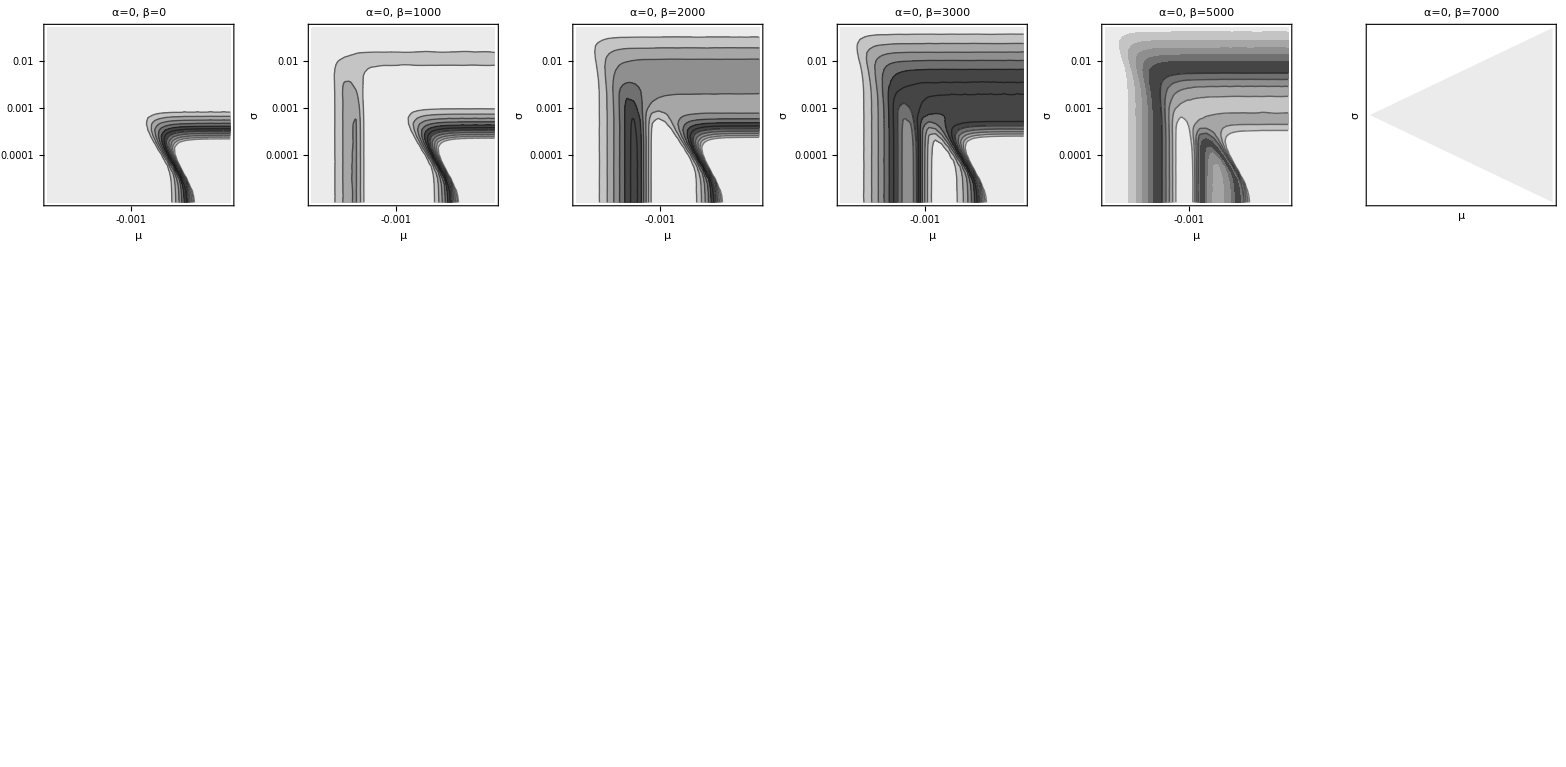

```mathematica
plotsRNS=GraphicsGrid[{{plotRNShetsA0B0,plotRNShetsA0B1000,plotRNShetsA0B2000,plotRNShetsA0B3000,plotRNShetsA0B5000,plotRNShetsA0B7000},{plotRNShetsA2B0,plotRNShetsA2B1000,plotRNShetsA2B2000,plotRNShetsA2B3000,plotRNShetsA2B5000,plotRNShetsA2B7000},{plotRNShetsA4B0,plotRNShetsA4B1000,plotRNShetsA4B2000,plotRNShetsA4B3000,plotRNShetsA4B5000,plotRNShetsA4B7000}},ImageSize->Full]
```

```mathematica
pointsRNSA0B0=Cases[Normal@ContourPlot[RNShetsintA0B0[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B1000=Cases[Normal@ContourPlot[RNShetsintA0B1000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B2000=Cases[Normal@ContourPlot[RNShetsintA0B2000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B3000=Cases[Normal@ContourPlot[RNShetsintA0B3000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B5000=Cases[Normal@ContourPlot[RNShetsintA0B5000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA0B7000=Cases[Normal@ContourPlot[RNShetsintA0B7000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B0=Cases[Normal@ContourPlot[RNShetsintA2B0[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B1000=Cases[Normal@ContourPlot[RNShetsintA2B1000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B2000=Cases[Normal@ContourPlot[RNShetsintA2B2000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B3000=Cases[Normal@ContourPlot[RNShetsintA2B3000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B5000=Cases[Normal@ContourPlot[RNShetsintA2B5000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA2B7000=Cases[Normal@ContourPlot[RNShetsintA2B7000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B0=Cases[Normal@ContourPlot[RNShetsintA4B0[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B1000=Cases[Normal@ContourPlot[RNShetsintA4B1000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B2000=Cases[Normal@ContourPlot[RNShetsintA4B2000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B3000=Cases[Normal@ContourPlot[RNShetsintA4B3000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B5000=Cases[Normal@ContourPlot[RNShetsintA4B5000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
pointsRNSA4B7000=Cases[Normal@ContourPlot[RNShetsintA4B7000[μ,σ]==0,{μ,-Log[Abs[-0.00001]],-Log[Abs[-0.05]]},{σ,Log[0.00001],Log[0.05]}],Line[pts_]->pts,Infinity];
```

```mathematica
plotsRNSpoints=GraphicsGrid[{{Show[plotRNShetsA0B0,ListPlot[pointsRNSA0B0,PlotStyle->White]],Show[plotRNShetsA0B1000,ListPlot[pointsRNSA0B1000,PlotStyle->White]],Show[plotRNShetsA0B3000,ListPlot[pointsRNSA0B3000,PlotStyle->White]],Show[plotRNShetsA0B5000,ListPlot[pointsRNSA0B5000,PlotStyle->White]],Show[plotRNShetsA0B7000,ListPlot[pointsRNSA0B7000,PlotStyle->White]]},{Show[plotRNShetsA2B0,ListPlot[pointsRNSA2B0,PlotStyle->White]],Show[plotRNShetsA2B1000,ListPlot[pointsRNSA2B1000,PlotStyle->White]],Show[plotRNShetsA2B3000,ListPlot[pointsRNSA2B3000,PlotStyle->White]],Show[plotRNShetsA2B5000,ListPlot[pointsRNSA2B5000,PlotStyle->White]],Show[plotRNShetsA2B7000,ListPlot[pointsRNSA2B7000,PlotStyle->White]]},{Show[plotRNShetsA4B0,ListPlot[pointsRNSA4B0,PlotStyle->White]],Show[plotRNShetsA4B1000,ListPlot[pointsRNSA4B1000,PlotStyle->White]],Show[plotRNShetsA4B3000,ListPlot[pointsRNSA4B3000,PlotStyle->White]],Show[plotRNShetsA4B5000,ListPlot[pointsRNSA4B5000,PlotStyle->White]],Show[plotRNShetsA4B7000,ListPlot[pointsRNSA4B7000,PlotStyle->White]]}},ImageSize->Full]
```

-Graphics-

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=0.txt",Flatten[pointsRNSA0B0,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=1000.txt",Flatten[pointsRNSA0B1000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=2000.txt",Flatten[pointsRNSA0B2000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=3000.txt",Flatten[pointsRNSA0B3000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=5000.txt",Flatten[pointsRNSA0B5000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=0_beta=7000.txt",Flatten[pointsRNSA0B7000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=0.txt",Flatten[pointsRNSA2B0,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=1000.txt",Flatten[pointsRNSA2B1000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=2000.txt",Flatten[pointsRNSA2B2000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=3000.txt",Flatten[pointsRNSA2B3000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=5000.txt",Flatten[pointsRNSA2B5000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-2_beta=7000.txt",Flatten[pointsRNSA2B7000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=0.txt",Flatten[pointsRNSA4B0,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=1000.txt",Flatten[pointsRNSA4B1000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=2000.txt",Flatten[pointsRNSA4B2000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=3000.txt",Flatten[pointsRNSA4B3000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=5000.txt",Flatten[pointsRNSA4B5000,1]//N];
```

```mathematica
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver14/Rai's/points/hets_points_rns_alpha=-4_beta=7000.txt",Flatten[pointsRNSA4B7000,1]//N];
```